ClebschGordan::phy: ThreeJSymbol[{2, -3}, {1, 0}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, 3}, {1, 0}, {3, -3}] is not physical.

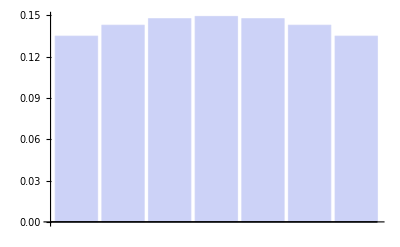

```mathematica
BarChart[Table[Total[Flatten[Table[(ThreeJSymbol[{F,m},{1,0},{3
,-m}])^2,{F,2,4}]]],{m,-3,3}]//N]
```

```mathematica
ThreeJSymbol[{3,0},{1,1},{3,-1}]
```

1/(√14)

ClebschGordan::phy: ThreeJSymbol[{2, 3}, {1, -1}, {3, -2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, 4}, {1, -1}, {3, -3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, 4}, {1, -1}, {3, -3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

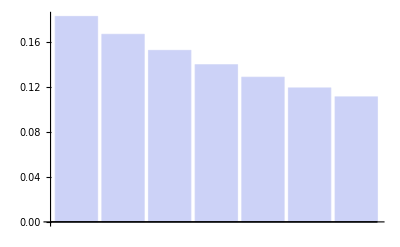

```mathematica
BarChart[Table[Total[Flatten[Table[(ThreeJSymbol[{F,m+1},{1,-1},{3
,-m}])^2,{F,2,4}]]],{m,-3,3}]//N]
```

ClebschGordan::phy: ThreeJSymbol[{2, -4}, {1, 1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, -4}, {1, 1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, -3}, {1, 1}, {3, 2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

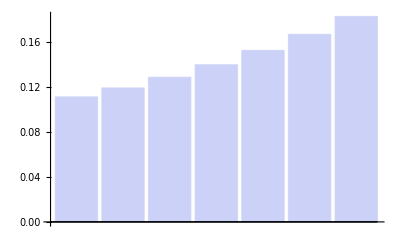

```mathematica
BarChart[Table[Total[Flatten[Table[(ThreeJSymbol[{F,m-1},{1,+1},{3
,-m}])^2,{F,2,4}]]],{m,-3,3}]//N]
```

```mathematica
(2 Sin[a-b]-Sin[b]+Sin[a]+Cosh[b]-Cos[a])^2+(-Sin[b]-Sin[a]-1)^2+(Cos[b]+Cos[a]+1)^2//Expand
```

```mathematica
Plot3D[(2 Sin[a-b]-Sin[b]+Sin[a]+Cosh[b]-Cos[a])^2+(-Sin[b]-Sin[a]-1)^2+(Cos[b]+Cos[a]+1)^2,{a,-Pi, Pi},{b,-Pi,Pi}, PlotLegends -> True]
```

-Graphics3D-

```mathematica
Plot3D[Abs[(2 Sin[a-b]-Sin[b]+Sin[a]+Cosh[b]-Cos[a])^1]+Abs[(-Sin[b]-Sin[a]-1)^1]+Abs[(Cos[b]+Cos[a]+1)^1],{a,0, Pi},{b,0,Pi}, PlotLegends -> True]
```

-Graphics3D-

-Graphics3D-

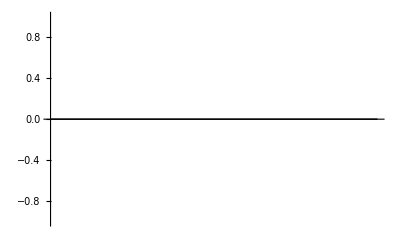

```mathematica
BarChart[Table[ThreeJSymbol[{3,m},{1,0},{F
,-m}],{m,-3,3}]]
```

ClebschGordan::tri: ThreeJSymbol[{3,0},{1,0},{5,0}] is not triangular.

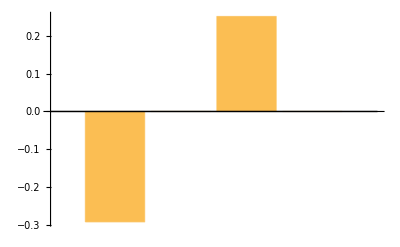

```mathematica
BarChart[Table[ThreeJSymbol[{3,0},{1,0},{F
,0}],{F,2,5}]]
```

```mathematica
Sqrt[2 (F ) + 1]*ThreeJSymbol[{F,m},{1,0},{F,-m}]//FullSimplify
```

Piecewise[{{((-1)^(1-F-m) m)/(√(F (1+F))), F-m∈Integers&&2 m∈Integers&&F+m∈Integers&&2 F≥1&&F≥m&&F+m≥0}, {0, True}}]

```mathematica
√(((F-m) (F+m))/(F (-1+2 F) (1+2 F)))//FullSimplify
```

√(-((F-m) (F+m))/(F-4 F^3))

```mathematica
Sqrt[2 (F-1)+1]*ThreeJSymbol[{F-1,m},{1,0},{F,-m}]//FullSimplify
```

Piecewise[{{(-1)^(F+m) √((F^2-m^2)/(F+2 F^2)), F-m∈Integers&&2 m∈Integers&&F+m∈Integers&&F≥1+m&&F+m≥1}, {0, True}}]

```mathematica
Sqrt[2 (F ) + 1]*ThreeJSymbol[{F,m-1},{1,1},{F,-m}]//FullSimplify
```

Piecewise[{{(-1)^(-F-m)/(√2 √((F (1+F))/(F+F^2+m-m^2))), F-m∈Integers&&2 m∈Integers&&F+m∈Integers&&F≥m&&F+m≥1}, {0, True}}]

```mathematica
Sqrt[2 (F -1) + 1]*ThreeJSymbol[{F,m-1},{1,1},{F-1,-m}]//FullSimplify
```

Piecewise[{{1/(√2)(-1)^(1-F-m) √(((F-m) (1+F-m))/(F (1+2 F))), F-m∈Integers&&2 m∈Integers&&F+m∈Integers&&F≥1+m&&F+m≥1}, {0, True}}]